DM, kolokvij 1, Jakob Valič

1. naloga

```mathematica
Maximize[x + y, {x + 2y≤1, y≥2x-7,x≥0,y≥-2}, {x,y}]
```

{2,{x→3,y→-1}}

Izraz je največji pri x = 3 in y = -1. Vrednost izraza je 2.

#### 2. naloga

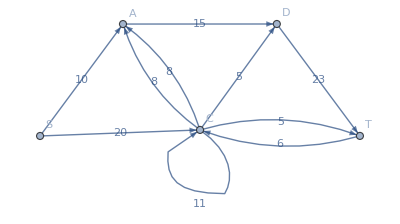

```mathematica
graf = 
Graph[{s->a,s->b,
a->d,
b->a,b->c,
c->a,c->d,c->t,
d->t,
t->b}, VertexLabels->{s->"S",a->"A", b->"B",c->"C",d->"D",t->"T"},
EdgeLabels->"EdgeWeight",EdgeWeight->{10,20,15,8,11,4,5,5,23,6}]
```

```mathematica
(M=WeightedAdjacencyMatrix[graf])//MatrixForm
```

(0 | 10 | 20 | 0 | 0
0 | 0 | 0 | 15 | 0
0 | 12 | 11 | 5 | 5
0 | 0 | 0 | 0 | 23
0 | 0 | 6 | 0 | 0)

```mathematica
FindMaximumFlow[M,1,6]
```

25

Največji pretok od vozlišča S do vozlišča T je 25.

```mathematica
3. naloga
```

3. naloga

```mathematica
A=({{2, -2, -3, -4}, {-1, 4, -3, -4}, {-1, -2, 8, -4}, {-1, -2, -3, 16}});
```

Matriki  A prištejemo poljubno vrednost tako, da bodo vse njene vrednosti nenegativne. Strategija igralcev se pri tem ne bo spremenila.

```mathematica
(A'=A+4) //MatrixForm
```

(6 | 2 | 1 | 0
3 | 8 | 1 | 0
3 | 2 | 12 | 0
3 | 2 | 1 | 20)

Nastavimo sistem za prvega igralca.

```mathematica
Minimize[{Subscript[u, 1]+Subscript[u, 2]+Subscript[u, 3]+Subscript[u, 4],
6 Subscript[u, 1]+3 Subscript[u, 2]+3 Subscript[u, 3]+3 Subscript[u, 4]≥1,
2 Subscript[u, 1]+8 Subscript[u, 2]+2 Subscript[u, 3]+2 Subscript[u, 4]≥1,
1 Subscript[u, 1]+1 Subscript[u, 2]+12 Subscript[u, 3]+1 Subscript[u, 4]≥1,
20 Subscript[u, 4]≥1,
Subscript[u, 1]≥0,Subscript[u, 2]≥0,Subscript[u, 4]≥0,Subscript[u, 4]≥0},
{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[u, 4]}]
```

{423/1600,{u_1→331/4800,u_2→377/4800,u_3→107/1600,u_4→1/20}}

Na podoben način bi lahko prišli do enakega rezultata tudi z ukazom LinearProgramming.

```mathematica
b=Table[1,Length[A]];
```

```mathematica
c=Table[1,Length[A]];
```

```mathematica
u'=LinearProgramming[c,Transpose[A'],b]
```

{331/4800,377/4800,107/1600,1/20}

Še za drugega igralca

```mathematica
v=LinearProgramming[-b,A',Partition[Riffle[c,Table[-1,{Length[c]}]],2]]
```

{11/80,11/160,3/80,33/1600}

```mathematica
ihω=v.Transpose[A'].u'
```

423/1600

Ker je vrednost igre > 0, je igra obrnjena v prid 1. igralcu. Poglejmo še s kakšno verjetnostjo naj igralca izbirata števila.

```mathematica
ω=1/ihω
p=ω u'//N
q=ω v//N
```

1600/423

{0.260835,0.297084,0.252955,0.189125}

{0.520095,0.260047,0.141844,0.0780142}

Igralec 1 bo izbral
1 z verjetnostjo 26,1 %
2 z verjetnostjo 29,7 %
3 z verjetnostjo 25,3 %
4 z verjetnostjo 18,9 %. Ima dokaj enakomerno porazdelitev svoje odločitve.

Igralec 2 se bo v večini primerov odločil za 1, nato za 2, 3 in nazadnje za 4. Pri 4 sicer lahko dobi 4  Eur, a hkrati največ tvega, ker v primeru, da 1. igralec ugane, izgubi 16 Eur.

#### 4. naloga

Označimo z a_x število naprav, ki jih prepeljemo iz skladišča A v skladišče X. Podobno storimo z drugimi spremenljivkami za skladišča. Nato začnemo pripravljati podatke za izračun.

Kriterijska funkcija je vsota, katere posamezen člen je število naprav, ki jih peljemo iz posamezne tovarne, pomnožen s ceno prevoza.

```mathematica
Clear[a,b,c]
```

```mathematica
kritFunkcija = 50 Subscript[a, x]+60 Subscript[a, y]+30 Subscript[a, z]+60 Subscript[b, x]+40 Subscript[b, y]+20 Subscript[b, z]+40 Subscript[c, x]+70 Subscript[c, y]+30 Subscript[c, z]
```

50 a_x+60 a_y+30 a_z+60 b_x+40 b_y+20 b_z+40 c_x+70 c_y+30 c_z

Pogoji, ki nam jih narekujejo število naprav, ki se nahajajo v tovarnah.

```mathematica
tovarne=Subscript[a, x]+Subscript[a, y]+Subscript[a, z]≤8,Subscript[b, x]+Subscript[b, y]+Subscript[b, z]≤5,Subscript[c, x]+Subscript[c, y]+Subscript[c, z]≤3
```

Število naprav, ki jih moramo prepeljati v skladišča.

```mathematica
skladišča=Subscript[a, x]+Subscript[b, x]+Subscript[c, x]=5,Subscript[a, y]+Subscript[b, y]+Subscript[c, y]=4,Subscript[a, z]+Subscript[b, z]+Subscript[c, z]=3
```

Dodamo še pogoje nenegativnosti. Pogoje za skladišča in tovarne kopiramo. Prav tako povemo, da želimo celoštevilsko rešitev.

```mathematica
Minimize[{ 50 Subscript[a, 1]+60 Subscript[a, 2]+30 Subscript[a, 3]+60 Subscript[b, 1]+40 Subscript[b, 2]+20 Subscript[b, 3]+40 Subscript[c, 1]+70 Subscript[c, 2]+30 Subscript[c, 3],
Subscript[a, 1]+Subscript[a, 2]+Subscript[a, 3]≤8,Subscript[b, 1]+Subscript[b, 2]+Subscript[b, 3]≤5,Subscript[c, 1]+Subscript[c, 2]+Subscript[c, 3]≤3,
Subscript[a, 1]+Subscript[b, 1]+Subscript[c, 1]=5,Subscript[a, 2]+Subscript[b, 2]+Subscript[c, 2]=4,Subscript[a, 3]+Subscript[b, 3]+Subscript[c, 3]=3,
Subscript[a, 1]>0,Subscript[a, 2]>0,Subscript[a, 3]>0,Subscript[b, 1]>0,Subscript[b, 2]>0,Subscript[b, 3]>0,Subscript[c, 1]>0,Subscript[c, 2]>0,Subscript[c, 3]>0},{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}]
```

Set::write: Tag Plus in a_1+b_1+c_1 is Protected.

Set::write: Tag Plus in a_2+b_2+c_2 is Protected.

Set::write: Tag Plus in a_3+b_3+c_3 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Minimize::consf: Invalid constraint 5 encountered. Constraints should be equations, inequalities, or variable domain specifications.

Minimize[{50 a_1+60 a_2+30 a_3+60 b_1+40 b_2+20 b_3+40 c_1+70 c_2+30 c_3,a_1+a_2+a_3≤8,b_1+b_2+b_3≤5,c_1+c_2+c_3≤3,5,4,3,a_1>0,a_2>0,a_3>0,b_1>0,b_2>0,b_3>0,c_1>0,c_2>0,c_3>0},{a_1,a_2,a_3,b_1,b_2,b_3,c_1,c_2,c_3}]

Spremeniti moramo še enačaje v dve neenačbi.